```mathematica
Needs["QuantumInformation`"];
Needs["MaTeX`"];
```

## CTAP on subdivided trees

#### Definitions for simulation

```mathematica
(* Tree construction methods *)

(* Given the root, this function returns (degree) leafs attached to the root *)
growLeafsFromRoot[ root_, degree_ ] := Module[{newvtx, newedges},
	newvtx = Table[ Append[ root, j ] , {j,0, degree-1} ];
	newedges = Table[ root <-> v, {v,newvtx} ];
	Return[{newvtx, newedges} ];
];

(* Given a set of roots, this function returns (degree) leafs grown from each of the roots *)
growLayerFromRoots[ roots_, degree_ ]:= Module[{newlayer, newvtxs, newedges},
	newlayer = Table[ growLeafsFromRoot[ root, degree ], {root, roots} ];
	(* newlayer has shape (nroots, 2), where the 2 represents (newvtx, newedges) *)
	newvtxs = Flatten[ newlayer[[All,1]], 1 ];
	newedges = Flatten[ newlayer[[All,2]], 1 ];
	Return[{newvtxs, newedges}];
];

(* Given a set of degrees, build the corresponding tree *)
growTree[ degrees_, root_:{} ] := Module[{nlayers, vtxlist, edgelist, newvtxs, newedges},

	nlayers = Length[degrees]+1;
	vtxlist ={  {root}   };
	edgelist = {};
	
	Do[
		{newvtxs, newedges} = growLayerFromRoots[ vtxlist[[-1]] , degrees[[l]]  ];
		AppendTo[ vtxlist, newvtxs ];
		AppendTo[ edgelist, newedges ];
		, {l, 1, nlayers-1}];
	Return[{vtxlist, edgelist} ];
];

(* Grow the subdivided tree specific for CTAP *)
SubdividedTreeGraph[ degrees_ ]:= Module[{subddegrees, vtxlist, edgelist },
	subddegrees = {degrees, ConstantArray[1, Length@degrees]}ᵀ // Flatten;
	{vtxlist, edgelist} = growTree[ subddegrees, {} ];
	Return[ Graph[ Flatten[vtxlist, 1] , Flatten[edgelist, 1 ] ] ];
];
```

```mathematica
(* CTAP simulation functions *)

CTAPerrorSingle[ ham_, aidx_, bidx_,{t_,Ti_, Tf_} ] := Module[{nq, state, err},

	nq = Length[ham];
	state = Normalize@evolveState[ ham, Vec[aidx-1, nq] ,{t,Ti, Tf}][Tf];
	err = 1-Abs[state.Vec[bidx-1, nq]];
	Return[err];
];


(* Assuming a flattened array with entries (p1, T, error), find for each p1 the optimal T *)
findTargetTimesFlat[ dataList_, targetEr_ ]:= Module[{allparams, filtered, bestT},
	
	allparams = DeleteDuplicates[ dataList[[All,1]] ];
	Return[ Table[
		filtered = Select[ dataList, #[[1]] == allparams[[j]] && #[[3]] ≤ targetEr & ];
		bestT = Min[ filtered[[All,2]] ];
		{allparams[[j]], bestT}
	,{j,1,Length[allparams]}] ];
];


addTimeDependence[ ham_, aidx_, bidx_, afun_,bfun_ ]:= Module[{ham2},
	ham2 = 1*ham;
	ham2[[aidx,All]] = afun * ham[[aidx,All]];
	ham2[[All,aidx]] = afun * ham[[All,aidx]];
	ham2[[bidx,All]] = bfun * ham[[bidx,All]];
	ham2[[All,bidx]] = bfun * ham[[All,bidx]];
	Return[ham2];
];
```

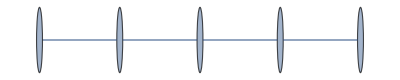

```mathematica
SubdividedTreeGraph[ {2} ]
```

#### Scaling with graph size test:

```mathematica
degree = 3;
nlevelss = Range[2,7];

res = Table[
degrees = ConstantArray[ degree, nlevels ];
g = SubdividedTreeGraph[ degrees ] ;
Ag = AdjacencyMatrix[g];
nq = Length@Ag;
idxm = Ceiling[nq/2]+1;
eval = Sort@Eigenvalues[N@ Ag ];
gap = eval[[idxm]];
{nlevels, nq,  degree^nlevels,gap}

, {nlevels, nlevelss}];
```

Eigenvalues::arh: Because finding 241 out of the 241 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

Eigenvalues::arh: Because finding 727 out of the 727 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

Eigenvalues::arh: Because finding 2185 out of the 2185 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

General::stop: Further output of Eigenvalues::arh will be suppressed during this calculation.

```mathematica
reslog = res * 1;
reslog[[All,1]] = 1/  Log@res[[All,1]];
```

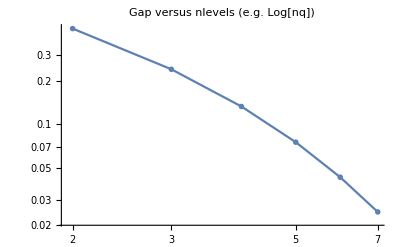
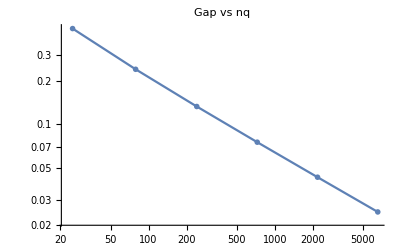

```mathematica
{ ListLogLogPlot[ res[[All,{1,4} ]], PlotLabel->"Gap versus nlevels (e.g. Log[nq])" ]
, ListLogLogPlot[ res[[All,{2,4} ]], PlotLabel->"Gap vs nq" ] }
```

```mathematica
degree = 2;
nlevels = 3;
degrees = ConstantArray[ degree, nlevels ];
straddle = 10;
g = SubdividedTreeGraph[ degrees ] ;
Ag = straddle * AdjacencyMatrix[g];
nq = Length@Ag;
nc = degree^nlevels;

Ts = 2^Range[2,7,.05];
aidx = nq;
bidx = nq-nc +1;

res = Table[
ham = addTimeDependence[ Ag, aidx, bidx,   t/T/straddle, ( 1-t/T )/straddle  ];
sol = evolveState2[ ham, Vec[ aidx-1, nq ], {t,0,T} ];
err = 1-(sol /. t-> T)[[bidx]];
{T,err}
,{T,Ts} ];
```

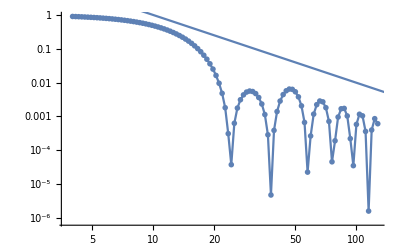

```mathematica
Show[{
ListLogLogPlot[res]
, LogLogPlot[ 100/x^2, {x,0,2000} ]
}]
```

#### Simulations and storing to file : Thanks to straddling, still find Sqrt[n]behaviour??!

NOTE:
Data 1 contained a bug.
Data 2 ???
Data 3 should now be used.

NOTE: We implement straddling as follows:
- the whole graph is multiplied by [straddle]
- the sender/receiver a/b have their connections rescaled to 1.

TODO: randomize weights a bit?
TODO: Scaling Sqrt[n] seems to break down at some point?

```mathematica
(* Setting up export options: Use convention (nlevels,  time,   error)  *)
degree = 5;
straddle = 4;
resultfile =  FileNameJoin[ {NotebookDirectory[] ,"data3", 
"CTAPtree_d" <> ToString[degree] <> "_s" <> ToString[straddle] <> ".dat"
}]; 

(* Specific settings *)
nlevelss = Range[1,6];
Ts = 2^Range[2,7,.2];

PrintTemporary["nlevels: ", nlevelss, " T: ", Ts ];
Monitor[
Do[
degrees = ConstantArray[ degree, nlevs ];
g = SubdividedTreeGraph[ degrees ] ;
Ag = straddle * AdjacencyMatrix[g];
nq = Length@Ag;
nc =  degree^nlevs;

aidx = nq;
bidx = If[ degree > 1, nq-nc +1 , 1 ];

 Do[
ham = addTimeDependence[ Ag, aidx, bidx, t/T/straddle, ( 1-t/T )/straddle  ];
sol = evolveState2[ ham, Vec[ aidx-1, nq ], {t,0,T} ];
err =  1-Abs[  (sol /. t-> T)[[bidx]]   ];
PutAppend[ {nlevs, T, err} , resultfile ];
,{T,Ts} ];

,{nlevs, nlevelss}];
, {nlevs, T} ]
```

#### Opening the data again

Read the Data

```mathematica
degree = 1;
straddle = 1;
resultfile =  FileNameJoin[ {NotebookDirectory[] ,"data3", "CTAPtree_d" <> ToString[degree] <> "_s" <> ToString[straddle] <> ".dat" }]; 
resall = ReadList[ resultfile ] ;

nlevelss = DeleteDuplicates@resall[[All,1]];
Ts = DeleteDuplicates@resall[[All,2]];
```

Evolution over time, for a specific nlevels

```mathematica
resfiltered2
```

{{400,1.07177,1.},{400,1.1487,1.},{400,1.23114,1.},{400,1.31951,1.},{400,1.41421,1.},{400,1.51572,1.},{400,1.6245,1.},{400,1.7411,1.},{400,1.86607,1.},{400,2.,1.},{400,2.14355,1.},{400,2.2974,1.},{400,2.46229,1.},{400,2.63902,1.},{400,2.82843,1.},{400,3.03143,1.},{400,3.24901,1.},{400,3.4822,1.},{400,3.73213,1.},{400,4.,1.},{400,4.,1.},{400,4.28709,1.},{400,4.59479,1.},{400,4.92458,1.},{400,5.27803,1.},{400,5.65685,1.},{400,6.06287,1.},{400,6.49802,1.},{400,6.9644,1.},{400,7.46426,1.},{400,8.,1.},{400,8.57419,1.},{400,9.18959,1.},{400,9.84916,1.},{400,10.5561,1.},{400,11.3137,1.},{400,12.1257,1.},{400,12.996,1.},{400,13.9288,1.},{400,14.9285,1.},{400,16.,1.},{400,17.1484,1.},{400,18.3792,1.},{400,19.6983,1.},{400,21.1121,1.},{400,22.6274,1.},{400,24.2515,1.},{400,25.9921,1.},{400,27.8576,1.},{400,29.8571,1.},{400,32.,1.},{400,34.2968,1.},{400,36.7583,1.},{400,39.3966,1.},{400,42.2243,1.},{400,45.2548,1.},{400,48.5029,1.},{400,51.9842,1.},{400,55.7152,1.},{400,59.7141,1.},{400,64.,1.},{400,68.5935,1.},{400,73.5167,1.},{400,78.7932,1.},{400,84.4485,1.},{400,90.5097,1.},{400,97.0059,1.},{400,103.968,1.},{400,111.43,1.},{400,119.428,1.},{400,128.,1.},{400,137.187,1.},{400,147.033,1.},{400,157.586,1.},{400,168.897,1.},{400,181.019,1.},{400,194.012,1.},{400,207.937,1.},{400,222.861,1.},{400,238.856,1.},{400,256.,1.}}

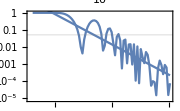
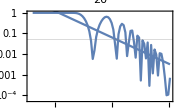
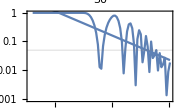
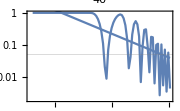
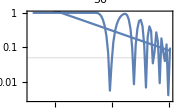
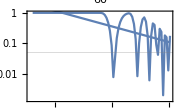
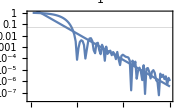
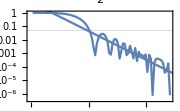

```mathematica
fitvals = {};
Row@Table[
picknlevels = l;
resfiltered = Select[ resall, #[[1]] == picknlevels & ];
resfiltered2 = SortBy[ resfiltered, #[[2]] & ];
{const, exp} = exponentFit[ resfiltered2[[All,{2,3}]] ];
AppendTo[ fitvals, { l, {const,exp} } ];
Show[{
ListLogLogPlot[ resfiltered2[[All,{2,3}]], GridLines->{{}, {.05}}
, Frame-> True
, PlotMarkers->None 
,PlotLabel->l
, ImageSize->Small]
,LogLogPlot[ const * x^exp , {x,0,Max[Ts]} ]
}]
,{l,nlevelss}]
```

```mathematica
Ag // Length
```

801

Extract T* from fitted Error Decay curves:

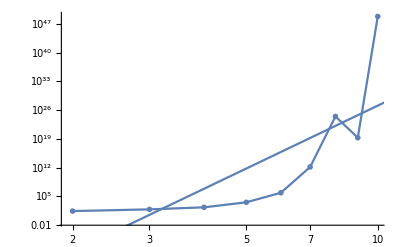

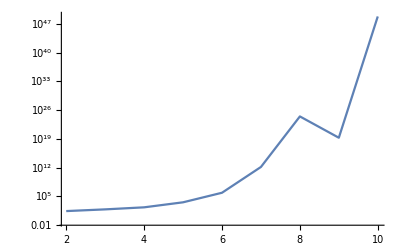

```mathematica
tartimesfit = Table[
{f[[1]], x /. First@Quiet@Solve[ f[[2,1]]* x^f[[2,2]] == 0.05 , x ] }
,{f,fitvals} ];
{const, exp} = exponentFit[ tartimesfit ];
Show[{
 ListLogLogPlot[ tartimesfit ]
,LogLogPlot[ const * x^exp , {x,0,Max[Ts]} ] 
}]
ListLogPlot[ tartimesfit , Joined -> True]
```

All in one plot

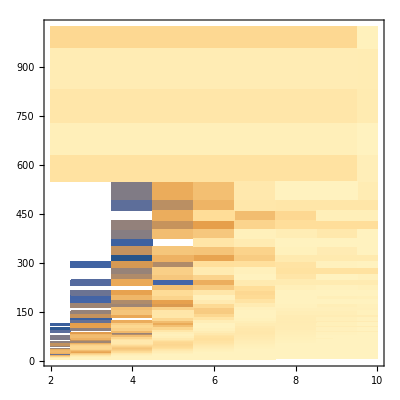

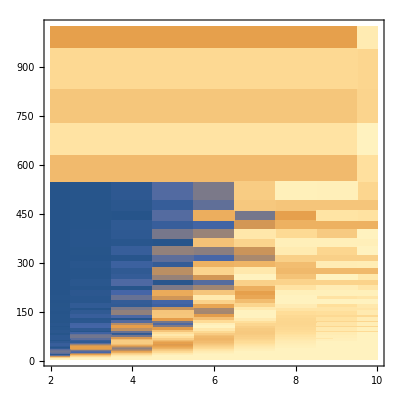

```mathematica
reslog = Table[ { e[[1]], e[[2]], Log@e[[3]] }, {e,resall} ];
ListContourPlot[ reslog, InterpolationOrder->0, Contours->1000 ]
ListContourPlot[ resall, InterpolationOrder->0, Contours -> 1000 ]
```

Target times

{1.33576,3.04595}

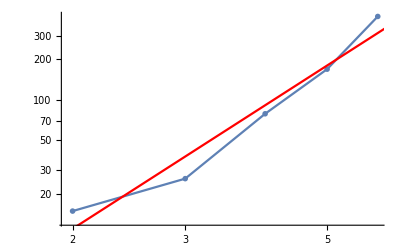

```mathematica
tartimes = findTargetTimesFlat[resall, .1 ];
fit = exponentFit[ tartimes ] 
Show[{
ListLogLogPlot[ tartimes ]
, LogLogPlot[ fit[[1]] * x ^ fit[[2]] , {x,1,Max[nlevelss]} , PlotStyle->Red, PlotLabel->"exponent: " <> ToString@fit[[2]] ]
}]
```

#### Effect of Straddling on Error*(T) dependence

```mathematica
file1 = "/export/scratch1/groenlan/Dropbox/PhD/MATHEMATICA/CTAP/test/CTAPtree_d2_s1.1.dat";
file2 = "/export/scratch1/groenlan/Dropbox/PhD/MATHEMATICA/CTAP/test/CTAPtree_d2_s1.5.dat";
file3 = "/export/scratch1/groenlan/Dropbox/PhD/MATHEMATICA/CTAP/test/CTAPtree_d2_s6.dat";

res1 = ReadList[ file1 ];
res2 = ReadList[ file2 ];
res3 = ReadList[ file3 ];

nlevelss1 = DeleteDuplicates@res1[[All,1]];
Ts1 = DeleteDuplicates@res1[[All,2]];
nlevelss2 = DeleteDuplicates@res2[[All,1]];
Ts2 = DeleteDuplicates@res2[[All,2]];
nlevelss3 = DeleteDuplicates@res3[[All,1]];
Ts3 = DeleteDuplicates@res3[[All,2]];
```

```mathematica
plotErrVsT[ resall_, nlevelss_, col_ ]:= Module[{},
Return@Table[
picknlevels = l;
resfiltered = Select[ resall, #[[1]] == picknlevels & ];
resfiltered2 = SortBy[ resfiltered, #[[2]] & ];

ListLogLogPlot[ resfiltered2[[All,{2,3}]], GridLines->{{}, {.1}}
, Frame-> True
, PlotMarkers->None 
,PlotLabel->l
, ImageSize->Small
, PlotStyle-> col[[l]] 
, Joined -> True
]

,{l,nlevelss}]

];
```

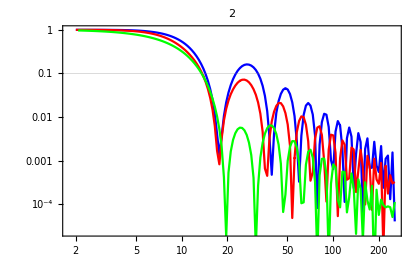
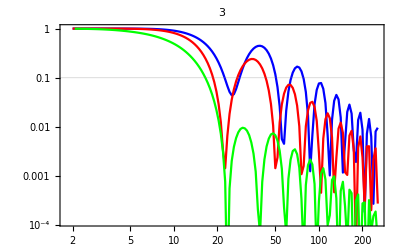
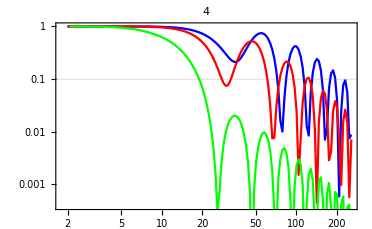
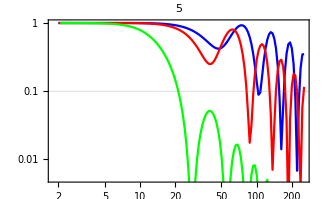
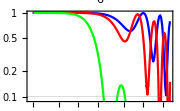
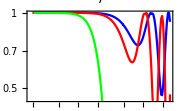

```mathematica
allreds = ConstantArray[ Red, 100];
allblue = ConstantArray[ Blue, 100];
allgreen = ConstantArray[Green, 100 ];

plts1 = plotErrVsT[ res1, nlevelss3, allblue ];
plts2 = plotErrVsT[ res2, nlevelss3, allreds ];
plts3 = plotErrVsT[ res3, nlevelss3, allgreen ];

Show /@  ( {plts1, plts2, plts3} ᵀ  )
```

## Pretty plot of states and energy levels

```mathematica
blend = 2/4;
elementarycols = {Darker@Red, Darker@Darker@Green,  Blend[  {Darker@Red, Yellow},blend ], Blend[ {Darker@Darker@Green, Blue}, blend ] };
brightcolours = {RGBColor[0.03529411764705882, 0.4392156862745098, 0.32941176470588235],RGBColor[0.396078431372549, 0.6, 1.],RGBColor[1., 0.8705882352941177, 0.],RGBColor[1., 0.6, 0.]};
textbookcolours = {RGBColor[0.028, 0.5376, 0.5936],Hue[0.07, 1, 0.75],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]};
colscheme10 = {RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.17254901960784313, 0.3607843137254902, 0.07058823529411765],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],RGBColor[0.3176470588235294, 0.49019607843137253, 0.0784313725490196],RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333],RGBColor[0.22745098039215686, 0.23921568627450981, 0.45098039215686275],RGBColor[0.09803921568627451, 0.06666666666666667, 0.25098039215686274],RGBColor[0.5607843137254902, 0.5254901960784314, 0.5647058823529412]};


(* Make very bare plots without units *)
plts = {Plot, ListPlot};
Do[
SetOptions[ plt
, BaseStyle -> {FontFamily-> "Helvetica", FontSize-> 20}
, Frame -> {True, True, True, True} 
, FrameStyle -> Directive[ Black, Thickness[0.003 ] ]
, PlotTheme-> None
, FrameTicksStyle-> Directive[ 15, Black ]
, FrameTicks -> Automatic
, ImageSize-> {500,200}
, AspectRatio-> Full
, GridLinesStyle -> Directive[ Gray, Thickness[ 0.005] ]
, PlotLegends -> Automatic
];
,{plt, plts}]
```

```mathematica
degree = 2;
nlevels = 2;
degrees = ConstantArray[ degree, nlevels ];
straddle = 1;
Ts = Range[10,100,1];
T = 300;

g = SubdividedTreeGraph[ degrees ] ;
Ag = straddle * AdjacencyMatrix[g];
nq = Length@Ag;
nc = degree^nlevels;

aidx = nq;
bidx = nq-nc +1;
idxm = Ceiling[nq/2];

(* res = Table[
ham = addTimeDependence[ Ag, aidx, bidx,   t/T/straddle, ( 1-t/T )/straddle  ];
sol = evolveState2[ ham, Vec[ aidx-1, nq ], {t,0,T} ];
err = 1-(sol /. t-> T)[[bidx]];
{T,err}
,{T,Ts} ];  *)
ham = addTimeDependence[ Ag, aidx, bidx,   t/T/straddle, ( 1-t/T )/straddle  ];
sol = evolveState2[ ham, Vec[ aidx-1, nq ], {t,0,T} ];
```

Plot the actual noisy state amplitudes

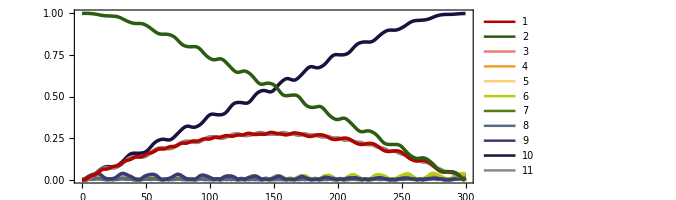

```mathematica
cols = colscheme10;
pltstyle = Table[ Directive[ {cols[[j]], Thickness[0.005] } ], {j, 1, Length[cols]} ];
Plot[ Evaluate@Abs@sol, {t,0,T} , PlotRange->{0,1}, PlotStyle->pltstyle ]
```

Plot the energy levels - in the perfect case

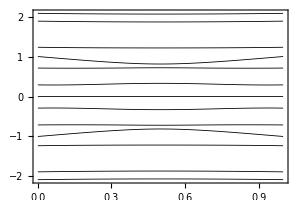

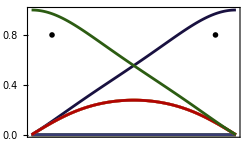

```mathematica
T = 1;
straddle = 1;
ham = addTimeDependence[ Ag, aidx, bidx,   t/T/straddle, ( 1-t/T )/straddle  ];

tvals = Range[ 0, T, T/100 ];

es=  Table[ 
{ConstantArray[ tval, nq ]
,Sort@Eigenvalues[ N[ Normal@ham  /. t -> tval ]  ]}ᵀ, {tval, tvals} ];

evecs = Table[
{eval, evec } = makeEigenSystem[ Normal@ham /. t-> tval ] ;
{ConstantArray[ tval, nq ],Abs@ evec[[idxm]]}ᵀ
,{tval, tvals} ];

treeElevels = ListPlot[esᵀ
, PlotMarkers->None
, PlotStyle->Directive[{Black, Thickness[0.002] }] 
, ImageSize-> {300,200}
, PlotLabel->MaTeX["\\text{Energy levels during protocol}", Magnification->1.3 ] 
 , FrameLabel->{MaTeX[ "t/T", Magnification->1.8 ], MaTeX["\\text{Energies} / J", Magnification->1.8]}
]

pltstyle = Table[ Directive[ {cols[[j]], Thickness[0.008] } ], {j, 1, Length[cols]} ];
treeStateAmp = ListPlot[ evecsᵀ 
, PlotMarkers->None
, PlotStyle->pltstyle
, ImageSize-> {250,150}
, PlotLegends->None
, FrameTicks -> { None, Automatic} 
, PlotLabel-> MaTeX["\\text{Absolute dark state amplitudes}", Magnification->1.3 ] 
, Epilog -> { 
Inset[ MaTeX[ "\\lvert a \\rangle", Magnification->1.8], {.1,.8}]
, Inset[ MaTeX[ "\\lvert b \\rangle", Magnification->1.8], {.9,.8}]  }
]
```

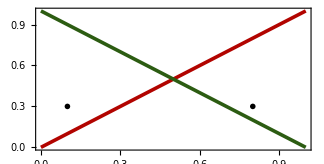

```mathematica
pltstyle = Table[ Directive[ {cols[[j]], Thickness[0.008] } ], {j, 1, Length[cols]} ];
treeControls = Plot[ {t, 1-t}, {t,0,1}
, PlotStyle->pltstyle
, ImageSize-> {300,150}
, FrameLabel->{MaTeX[ "t/T", Magnification->1.8 ], MaTeX["J", Magnification->1.8]}
, PlotLegends->None
, Epilog -> { 
Inset[ MaTeX[ "f_a", Magnification->1.8], {.1,.3}]
, Inset[ MaTeX[ "f_b", Magnification->1.8], {.8,.3}]  }
(* , FrameTicks -> { {{0,1},None}, {{0,1}, None} }  *)
 ]
```

```mathematica
Export[ "treeElevels.pdf", treeElevels];
Export["treeStateAmp.pdf", treeStateAmp];
Export["treeControls.pdf", treeControls];
```